# CRMSD and D

## data loading

```mathematica
p0s={3.85,3.825,3.80,3.775,3.75};
```

```mathematica
temperatures={{0.039 ,0.016, 0.01 ,0.005 ,0.00385, 0.0025 ,0.002, 0.001 ,0.0005 ,0.00033 ,0.00025, 0.00014, 0.000091,0.000077,0.000054, 0.000045, 0.000036},{0.063 ,0.039, 0.03105, 0.016 ,0.01, 0.008, 0.0063, 0.005 ,0.00385, 0.0031, 0.0025, 0.002, 0.0015, 0.001, 0.00067 ,0.0005},{0.063 ,0.039 ,0.03105, 0.025, 0.016 ,0.01 ,0.008 ,0.0063, 0.005, 0.00385, 0.0031, 0.0028 ,0.0025 ,0.0022},{0.03105, 0.025 ,0.02 ,0.016 ,0.012, 0.01, 0.009 ,0.008 ,0.0075, 0.007 ,0.0063, 0.0056 ,0.0054},{0.063, 0.039, 0.03105, 0.025 ,0.02, 0.016, 0.014,0.012 ,0.011, 0.01, 0.0093}};
 records={{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19}};
tauEstimate={{2, 4,10, 20, 40,60, 80, 200, 500, 800, 1400, 2500, 4200,5000, 6000, 8500, 9500},{1, 2, 4 ,9 ,15,25, 40 ,60, 80, 120,200 ,300 ,1000 ,1500, 5000,10000},{1, 3, 4 ,8 ,15,40 ,70 ,150 ,250, 600 ,2000, 2500 ,4500, 9500},{2, 10,20 ,30, 80 ,100 ,400 ,500 ,2500 ,2500, 3000 ,7000, 10000},{4 ,5 ,7 ,10 ,30 ,70, 150 ,700,1400, 4000 ,9500}};
```

```mathematica
CRMSDs=Table[Table[DeleteCases[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p","/timeCRMSD_N4096_p","_T","_waitingTime","_idx",".nc"},{p0s[[p]],p0s[[p]],temperatures[[p,T]],If[tauEstimate[[p,T]]<1000,10000,tauEstimate[[p,T]]*10],records[[p,i]]},{3,4,8,0,0}],"Data"],{i,Length[records[[p]]]}],$Failed],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.800/timeCRMSD_N4096_p3.8000_T0.06300000_waitingTime10000_idx14.nc not found during Import.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.800/timeCRMSD_N4096_p3.8000_T0.06300000_waitingTime10000_idx15.nc not found during Import.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.800/timeCRMSD_N4096_p3.8000_T0.06300000_waitingTime10000_idx17.nc not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

```mathematica
MSDs=Table[Table[DeleteCases[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p","/timeMSD_N4096_p","_T","_waitingTime","_idx",".nc"},{p0s[[p]],p0s[[p]],temperatures[[p,T]],If[tauEstimate[[p,T]]<1000,10000,tauEstimate[[p,T]]*10],records[[p,i]]},{3,4,8,0,0}],"Data"],{i,Length[records[[p]]]}],$Failed],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.800/timeMSD_N4096_p3.8000_T0.06300000_waitingTime10000_idx14.nc not found during Import.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.800/timeMSD_N4096_p3.8000_T0.06300000_waitingTime10000_idx15.nc not found during Import.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.800/timeMSD_N4096_p3.8000_T0.06300000_waitingTime10000_idx17.nc not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

```mathematica
CRTrueMSDs=Table[Table[DeleteCases[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p","/timeTrueCRMSD_N4096_p","_T","_waitingTime","_idx",".nc"},{p0s[[p]],p0s[[p]],temperatures[[p,T]],If[tauEstimate[[p,T]]<1000,10000,tauEstimate[[p,T]]*10],records[[p,i]]},{3,4,8,0,0}],"Data"],{i,Length[records[[p]]]}],$Failed],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.800/timeTrueCRMSD_N4096_p3.8000_T0.06300000_waitingTime10000_idx14.nc not found during Import.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.800/timeTrueCRMSD_N4096_p3.8000_T0.06300000_waitingTime10000_idx15.nc not found during Import.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.800/timeTrueCRMSD_N4096_p3.8000_T0.06300000_waitingTime10000_idx17.nc not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

```mathematica
trueMSDs=Table[Table[DeleteCases[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p","/timeTrueMSD_N4096_p","_T","_waitingTime","_idx",".nc"},{p0s[[p]],p0s[[p]],temperatures[[p,T]],If[tauEstimate[[p,T]]<1000,10000,tauEstimate[[p,T]]*10],records[[p,i]]},{3,4,8,0,0}],"Data"],{i,Length[records[[p]]]}],$Failed],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

General::stop: Further output of Import::nffil will be suppressed during this calculation.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.800/timeTrueMSD_N4096_p3.8000_T0.06300000_waitingTime10000_idx17.nc not found during Import.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.800/timeTrueMSD_N4096_p3.8000_T0.06300000_waitingTime10000_idx15.nc not found during Import.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.800/timeTrueMSD_N4096_p3.8000_T0.06300000_waitingTime10000_idx14.nc not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.800/timeTrueMSD_N4096_p3.8000_T0.06300000_waitingTime10000_idx17.nc not found during Import.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.800/timeTrueMSD_N4096_p3.8000_T0.06300000_waitingTime10000_idx15.nc not found during Import.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.800/timeTrueMSD_N4096_p3.8000_T0.06300000_waitingTime10000_idx14.nc not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.800/timeTrueMSD_N4096_p3.8000_T0.06300000_waitingTime10000_idx17.nc not found during Import.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.800/timeTrueMSD_N4096_p3.8000_T0.06300000_waitingTime10000_idx15.nc not found during Import.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.800/timeTrueMSD_N4096_p3.8000_T0.06300000_waitingTime10000_idx14.nc not found during Import.

Import::nffil: File \"\</home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.800/timeTrueMSD_N4096_p3.8000_T0.06300000_waitingTime10000_idx14.nc\>\" not found during Import.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.800/timeTrueMSD_N4096_p3.8000_T0.06300000_waitingTime10000_idx15.nc not found during Import.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.800/timeTrueMSD_N4096_p3.8000_T0.06300000_waitingTime10000_idx17.nc not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

```mathematica
Length[CRMSDs[[1,1]]]
```

10

```mathematica
CRMSDMean=Table[Table[Table[Mean[DeleteCases[Table[CRMSDs[[p,T,i,2,rec]],{i,Length[CRMSDs[[p,T]]]}],_Missing|_Part]],{rec,Max[Table[Length[CRMSDs[[p,T,i,1]]],{i,Length[CRMSDs[[p,T]]]}]]-3}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

Part::partw: Part 104 of … does not exist.

Part::partw: Part 105 of … does not exist.

Part::partw: Part 106 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
MSDMean=Table[Table[Table[Mean[DeleteCases[Table[MSDs[[p,T,i,2,rec]],{i,Length[MSDs[[p,T]]]}],_Missing|_Part]],{rec,Max[Table[Length[MSDs[[p,T,i,1]]],{i,Length[MSDs[[p,T]]]}]]-3}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

Part::partw: Part 104 of … does not exist.

Part::partw: Part 105 of … does not exist.

Part::partw: Part 106 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
CRTrueMSDMean=Table[Table[Table[Mean[DeleteCases[Table[CRTrueMSDs[[p,T,i,2,rec]],{i,Length[CRTrueMSDs[[p,T]]]}],_Missing|_Part]],{rec,Max[Table[Length[CRTrueMSDs[[p,T,i,1]]],{i,Length[CRTrueMSDs[[p,T]]]}]]-3}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

Part::partw: Part 103 of … does not exist.

Part::partw: Part 104 of … does not exist.

Part::partw: Part 105 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 104 of (*InterpretationBox[RowBox[{TagBox[\"NumericArray\",\"SummaryHead\"], \"[\", DynamicModuleBox[{Typeset`open$$ = False, Typeset`embedState$$ = \"Ready\"}, TemplateBox[{PaneSelectorBox[{False -> GridBox[{{PaneBox[ButtonBox[DynamicBox[FEPrivate`FrontEndResource[\"FEBitmaps\", \"SummaryBoxOpener\"], ImageSizeCache -> {9.581249999999999, {0., 9.581249999999999}}], Appearance -> None, BaseStyle -> {}, ButtonFunction :> (Typeset`open$$ = True), Evaluator -> Automatic, Method -> \"Preemptive\"], Alignment -> {Center, Center}, ImageSize -> Dynamic[{Automatic, 3.5 (CurrentValue[\"FontCapHeight\"]/AbsoluteCurrentValue[Magnification])}]], GridBox[{{RowBox[{TagBox[\"\\\"Type: \\\"\", \"SummaryItemAnnotation\"], \"\", TagBox[\"\\\"Real64\\\"\", \"SummaryItem\"]}]}, {RowBox[{TagBox[\"\\\"Dimensions: \\\"\", \"SummaryItemAnnotation\"], \"\", TagBox[RowBox[{\"{\", \"102\", \"}\"}], \"SummaryItem\"]}]}}, AutoDelete -> False, BaseStyle -> {ShowStringCharacters -> False, NumberMarks -> False, PrintPrecision -> 3, ShowSyntaxStyles -> False}, GridBoxAlignment -> {\"Columns\" -> {{Left}}, \"Rows\" -> {{Automatic}}}, GridBoxItemSize -> {\"Columns\" -> {{Automatic}}, \"Rows\" -> {{Automatic}}}, GridBoxSpacings -> {\"Columns\" -> {{2}}, \"Rows\" -> {{Automatic}}}]}}, AutoDelete -> False, BaselinePosition -> {1, 1}, GridBoxAlignment -> {\"Columns\" -> {{Left}}, \"Rows\" -> {{Top}}}, GridBoxItemSize -> {\"Columns\" -> {{Automatic}}, \"Rows\" -> {{Automatic}}}], True -> GridBox[{{PaneBox[ButtonBox[DynamicBox[FEPrivate`FrontEndResource[\"FEBitmaps\", \"SummaryBoxCloser\"]], Appearance -> None, BaseStyle -> {}, ButtonFunction :> (Typeset`open$$ = False), Evaluator -> Automatic, Method -> \"Preemptive\"], Alignment -> {Center, Center}, ImageSize -> Dynamic[{Automatic, 3.5 (CurrentValue[\"FontCapHeight\"]/AbsoluteCurrentValue[Magnification])}]], GridBox[{{RowBox[{TagBox[\"\\\"Type: \\\"\", \"SummaryItemAnnotation\"], \"\", TagBox[\"\\\"Real64\\\"\", \"SummaryItem\"]}]}, {RowBox[{TagBox[\"\\\"Dimensions: \\\"\", \"SummaryItemAnnotation\"], \"\", TagBox[RowBox[{\"{\", \"102\", \"}\"}], \"SummaryItem\"]}]}, {RowBox[{TagBox[\"\\\"Data: \\\"\", \"SummaryItemAnnotation\"], \"\", TagBox[TemplateBox[{\"1.5142901238943776`*^-7\", \"\\\", \\\"\", \"\\\"…\\\"\"}, \"RowDefault\"], \"SummaryItem\"]}]}}, AutoDelete -> False, BaseStyle -> {ShowStringCharacters -> False, NumberMarks -> False, PrintPrecision -> 3, ShowSyntaxStyles -> False}, GridBoxAlignment -> {\"Columns\" -> {{Left}}, \"Rows\" -> {{Automatic}}}, GridBoxItemSize -> {\"Columns\" -> {{Automatic}}, \"Rows\" -> {{Automatic}}}, GridBoxSpacings -> {\"Columns\" -> {{2}}, \"Rows\" -> {{Automatic}}}]}}, AutoDelete -> False, BaselinePosition -> {1, 1}, GridBoxAlignment -> {\"Columns\" -> {{Left}}, \"Rows\" -> {{Top}}}, GridBoxItemSize -> {\"Columns\" -> {{Automatic}}, \"Rows\" -> {{Automatic}}}]}, Dynamic[Typeset`open$$], ImageSize -> Automatic]},\"SummaryPanel\"],DynamicModuleValues:>{}], \"]\"}],RawArray[\"Real64\",{1.5142901238943776`*^-7, 6.05716490343611*^-7, 1.3628216235829423`*^-6, 2.4226478360567967`*^-6, 3.7850421679359993`*^-6, 5.4497946247752485`*^-6, 7.4166341479738284`*^-6, 9.685229173030118*^-6, 0.000012255191132303566`, 0.000015126068349501532`, 0.000018297347409712073`, 0.00002553876140296778, 0.000029607566127053012`, 0.00003863757218497752, 0.000048851579077150296`, 0.000060241622580474745`, 0.00007279871151362824, 0.00009380025308146543, 0.0001173663922567682, 0.00015270041530182426`, 0.0001820699075411371, 0.0002363146929534598, 0.00029692305406661744`, 0.0003635693797170636, 0.000451015181221374, 0.0005625158137464158, 0.0007011639956793232, 0.000850330445611448, 0.0010495155231700043`, 0.00128257701473755, 0.001551282209463116, 0.001882022777577365, 0.002256095287271152, 0.0027047648501206827`, 0.0032685577205928133`, 0.003940666611346297, 0.004746140028555596, 0.005743326049916972, 0.006983003316181581, 0.008432964435989117, 0.010220478381621639`, 0.012360685285911442`, 0.014965639406892363`, 0.01794831359793317, 0.02147465335090447, 0.02574278199404481, 0.030643071555691747`, 0.036110218907299006`, 0.042298875636196206`, 0.04887749095106443, 0.05547446641254454, 0.06256504382816307, 0.06929909128032569, 0.07589972627384695, 0.08113091184907008, 0.08554303735404217, 0.08907766209823868, 0.09033209326139136, 0.0903854931791074, 0.08889280954173255, 0.08798294380612542, 0.08742940085766446, 0.08790303519725638, 0.0889971820825513, 0.09051742895102029, 0.0897778814258681, 0.08788096387564714, 0.08818699368940906, 0.08942607774659027, 0.09101881826774139, 0.08867553397886127, 0.09391005142290416, 0.09514609743111, 0.09738671535241791, 0.09761924698863544, 0.09949169844537628, 0.09969107576403934, 0.10444037306131952`, 0.1083612413681997, 0.10870783023352149`, 0.11048530344377747`, 0.11768892031946797`, 0.11830202643528862`, 0.12485159118699946`, 0.12729213704536063`, 0.1336972008076427, 0.13627516556671215`, 0.13885175223441545`, 0.14338892629759098`, 0.15718518715844548`, 0.15776053870065707`, 0.15999792849629724`, 0.17084758155035348`, 0.17077236277767474`, 0.185003306510776, 0.19177240949902735`, 0.21220085435779554`, 0.22784850723538047`, 0.2425752342706695, 0.2578319448599601, 0.2753238382321741, 0.2934375136823309}],Editable->False,SelectWithContents->True,Selectable->False]) does not exist.

Part::partw: Part 105 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
trueMSDMean=Table[Table[Table[Mean[DeleteCases[Table[trueMSDs[[p,T,i,2,rec]],{i,Length[trueMSDs[[p,T]]]}],_Missing|_Part]],{rec,Max[Table[Length[trueMSDs[[p,T,i,1]]],{i,Length[trueMSDs[[p,T]]]}]]-3}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

Part::partw: Part 103 of … does not exist.

Part::partw: Part 104 of … does not exist.

Part::partw: Part 105 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
time=Table[Table[Table[Mean[DeleteCases[Table[CRMSDs[[p,T,i,1,rec]],{i,Length[CRMSDs[[p,T]]]}],_Missing|_Part]],{rec,Max[Table[Length[CRMSDs[[p,T,i,1]]],{i,Length[CRMSDs[[p,T]]]}]]-3}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

Part::partw: Part 104 of … does not exist.

Part::partw: Part 105 of … does not exist.

Part::partw: Part 106 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

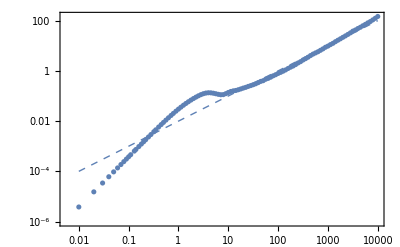

```mathematica
Show[ListLogLogPlot[Table[{CRMSDs[[3,1,1,1,rec]]-CRMSDs[[1,1,1,1,1]],CRMSDs[[4,4,1,2,rec]]},{rec,Length[CRMSDs[[1,1,1,1]]]}]],LogLogPlot[.01x,{x,0.01,10000},PlotStyle->{Dashed,Thick}]]
```

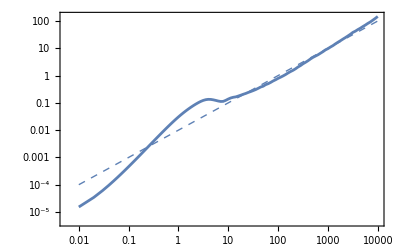

```mathematica
Show[ListLogLogPlot[Table[{CRTrueMSDs[[1,1,1,1,rec+1]]-CRTrueMSDs[[1,1,1,1,1]],CRTrueMSDs[[4,4,1,2,rec]]},{rec,Length[CRTrueMSDs[[1,1,1,1]]]-1}],Joined->True],LogLogPlot[.01x,{x,0.01,10000},PlotStyle->{Dashed,Thick}]]
```

```mathematica
Normal[CRTrueMSDs[[3,1,1,1]]-CRTrueMSDs[[1,1,1,1,1]]][[;;15]]
```

{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.12,0.13,0.15,0.17}

```mathematica
Normal[CRMSDs[[4,4,1,2]]][[;;15]]
```

{0.,3.81411×10^-6,0.0000152537,0.0000343128,0.0000609828,0.000095252,0.000137107,0.00018653,0.000243504,0.000308007,0.000380016,0.000459503,0.000640796,0.000742533,0.000968001}

```mathematica
Normal[CRTrueMSDs[[4,4,1,2]]][[;;15]]
```

{3.81411×10^-6,0.0000152537,0.0000343128,0.0000609828,0.000095252,0.000137107,0.00018653,0.000243504,0.000308007,0.000380016,0.000459503,0.000640796,0.000742533,0.000968001,0.00122252}

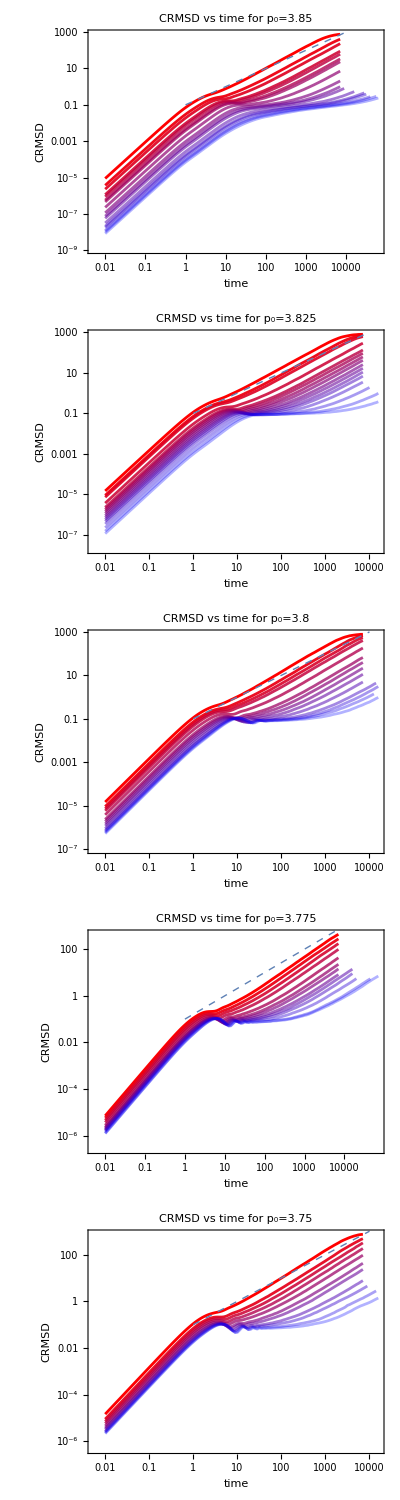

```mathematica
CRMSDMeanPlots=Table[Show[
ListLogLogPlot[Table[Table[{time[[p,T,rec]]-time[[p,T,1]],CRMSDMean[[p,T,rec]]},{rec,Length[CRMSDMean[[p,T]]]}],{T,Length[temperatures[[p]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]],FrameLabel->{"time","CRMSD"},ImageSize->600,PlotLabel->"CRMSD vs time for p_0="<>ToString[p0s[[p]]],Joined->True],LogLogPlot[.1x,{x,1,10000},PlotStyle->{Dashed,Thick}]],{p,Length[p0s]}];
Column[CRMSDMeanPlots]
```

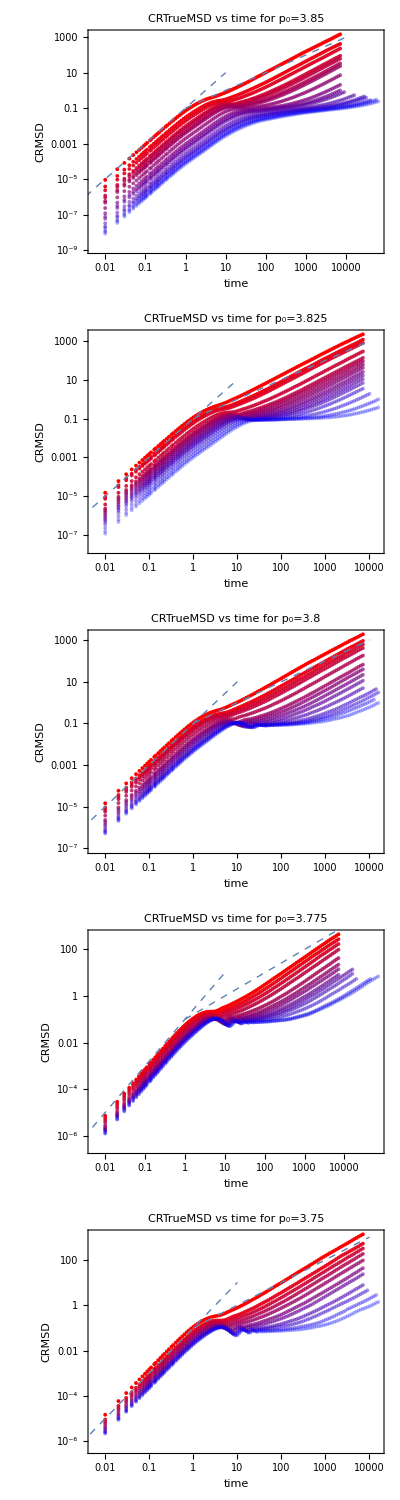

```mathematica
CRMSDTrueMeanPlots=Table[Show[
ListLogLogPlot[Table[Table[{time[[p,T,rec+1]]-time[[p,T,1]],CRTrueMSDMean[[p,T,rec]]},{rec,Length[CRTrueMSDMean[[p,T]]]}],{T,Length[temperatures[[p]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]],FrameLabel->{"time","CRMSD"},ImageSize->600,PlotLabel->"CRTrueMSD vs time for p_0="<>ToString[p0s[[p]]],Joined->False],LogLogPlot[.1x,{x,1,10000},PlotStyle->{Dashed,Thick}],LogLogPlot[.1x^2,{x,0.001,10},PlotStyle->{Dashed,Thick}]],{p,Length[p0s]}];
Column[CRMSDTrueMeanPlots]
```

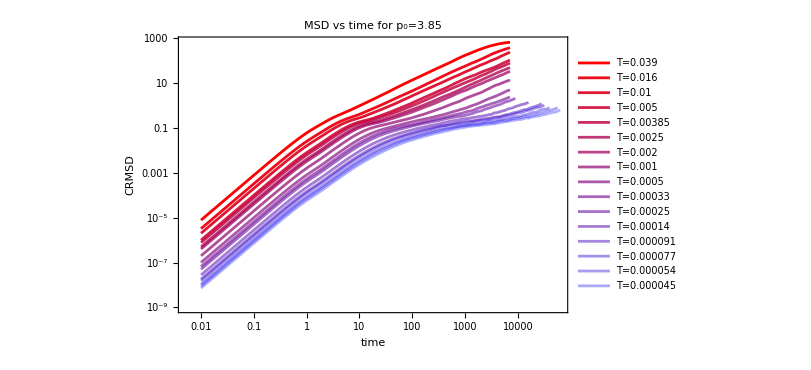
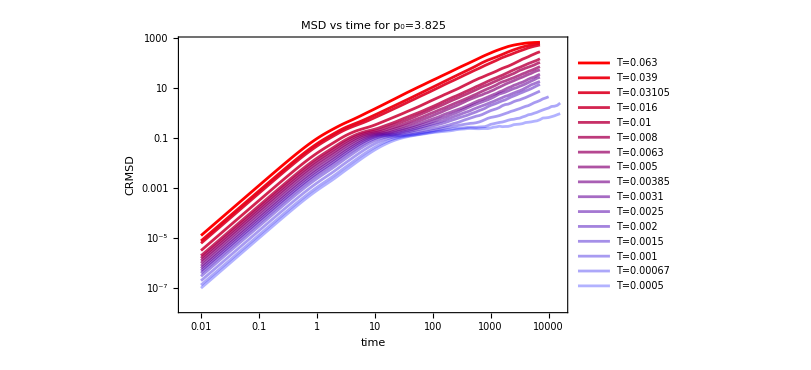
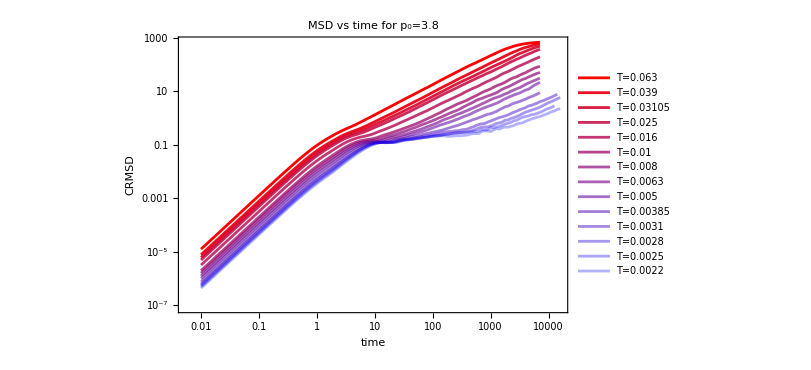
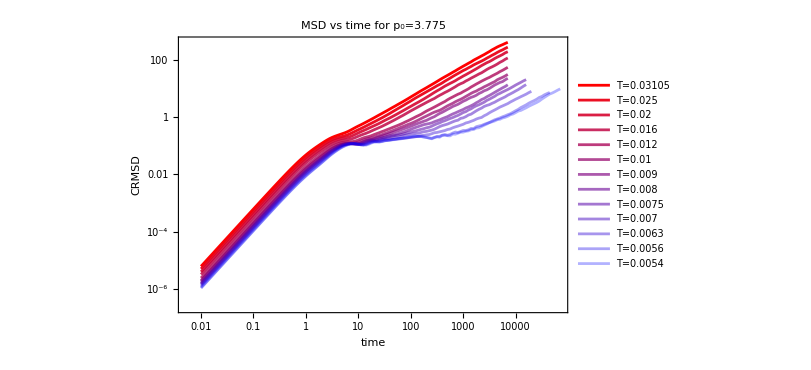
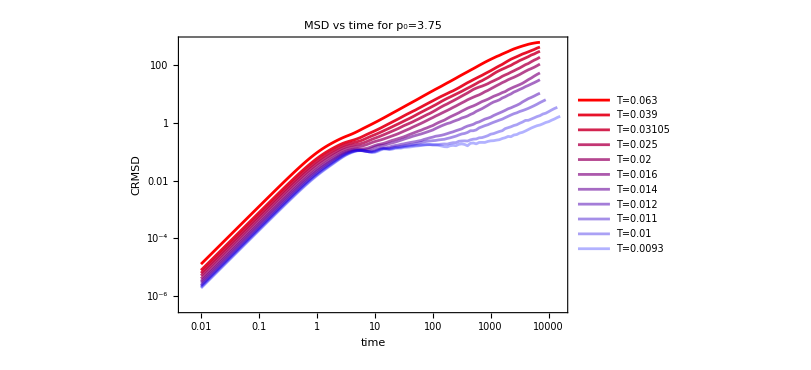

```mathematica
MSDMeanPlots=Table[
ListLogLogPlot[Table[Table[{time[[p,T,rec]]-time[[p,T,1]],MSDMean[[p,T,rec]]},{rec,Length[CRMSDMean[[p,T]]]}],{T,Length[temperatures[[p]]]}],PlotLegends->Table["T="<>ToString[temperatures[[p]][[T]]],{T,Length[temperatures[[p]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]],FrameLabel->{"time","CRMSD"},ImageSize->600,PlotLabel->"MSD vs time for p_0="<>ToString[p0s[[p]]],Joined->True],{p,Length[p0s]}];
Column[MSDMeanPlots]
```

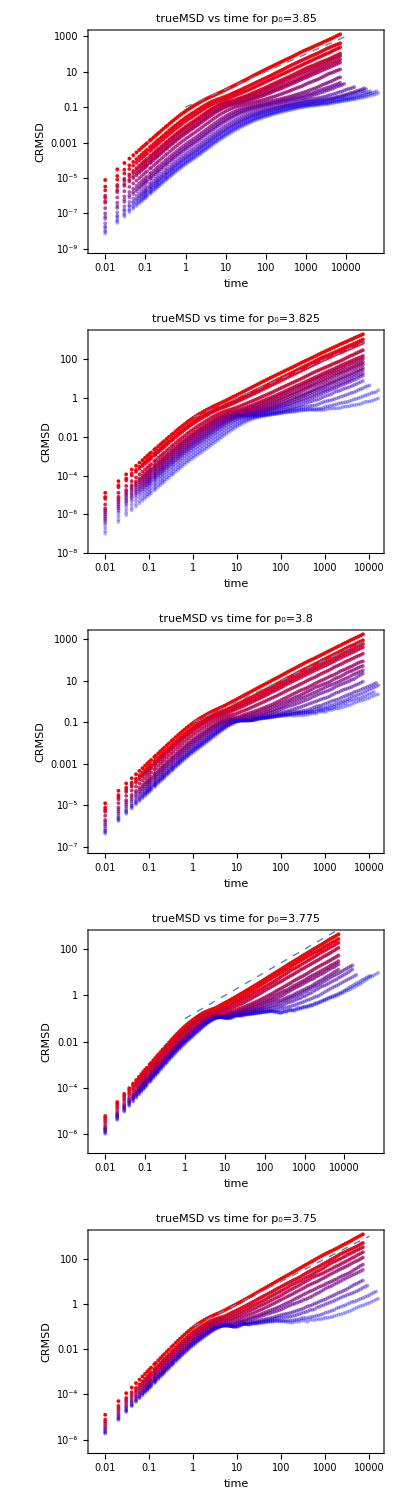

```mathematica
trueMSDMeanPlots=Table[Show[
ListLogLogPlot[Table[Table[{time[[p,T,rec+1]]-time[[p,T,1]],trueMSDMean[[p,T,rec]]},{rec,Length[trueMSDMean[[p,T]]]}],{T,Length[temperatures[[p]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]],FrameLabel->{"time","CRMSD"},ImageSize->600,PlotLabel->"trueMSD vs time for p_0="<>ToString[p0s[[p]]],Joined->False],LogLogPlot[.1x,{x,1,10000},PlotStyle->{Dashed,Thick}]],{p,Length[p0s]}];
Column[trueMSDMeanPlots]
```

```mathematica
(*MSD in Daniel's paper*)
MSDpaper={{0.02744749241872213,0.0007787583475777915},
{0.0514315895080298,0.0014551103426274877},
{0.1000000000000001,0.0026078919439150756},
{0.23387508439166665,0.005080218046913028},
{0.40702929570271873,0.0080348426383541},
{0.7626985859023452,0.012707859313704488},
{1.538741884408703,0.020098674685430508},
{2.7787550653702198,0.028051998106045035},
{5.606129189998862,0.03915256155232898},
{9.756741816936332,0.048223410150691405},
{19.684194472866192,0.05939578904572267},
{28.480358684358105,0.06730608019616548},
{66.60846290809181,0.09010546478929268},
{120.2856733658804,0.115704011481292},
{187.38174228603867,0.1425102670302998},
{291.904400246814,0.18299677618038562},
{438.2392079060478,0.23498531572671966},
{634.0726742929744,0.30174355942071884},
{917.4171298046817,0.40395672411076433},
{1377.3281798599119,0.5407937629806314},
{2067.797573651249,0.7869145977415526},
{2991.8225338310194,1.053475486498788},
{4328.761281083071,1.470350299935503},
{6263.130254791473,2.052188239999369},
{9402.904648067826,2.9861603330415765},
{13111.339374215684,4.167825258028193},
{18970.329150362097,5.817091329374349},
{29552.092352028998,8.82472859400099},
{59621.24896322193,17.922296801258483}};
```

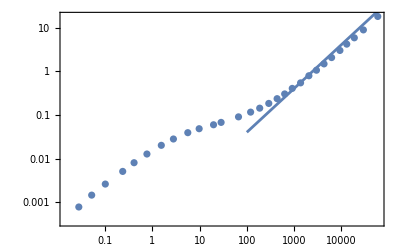

```mathematica
Show[ListLogLogPlot[Table[{MSDpaper[[i,1]],MSDpaper[[i,2]]},{i,Length[MSDpaper]}]],LogLogPlot[0.0004x,{x,100,100000}]]
```

### Fit to MSD~At^B

```mathematica
powerLaw[x_,A_,B_]:=2 A x^B;
```

```mathematica
fittingOffsetfromEnd={{15,15,15,10,10,10,10,8,5,5,5,5,5,5,5,5,5,5},{20,20,20,20,15,15,10,10,10,10,8,8,8,5,5,5},{20,20,20,20,20,10,10,10,10,10,5,5,5,5,5,5},{20,20,20,20,10,10,10,10,15,15,15,8,8},{20,20,20,20,20,20,20,5,5,5,5,5}};
```

```mathematica
fittingOffsetfromEnd={{15,15,15,10,10,10,10,8,5,5,5,5,5,5,5,5,5,5},{15,15,15,15,15,15,10,10,10,10,8,8,8,5,5,5},{15,15,15,15,15,10,10,10,10,10,5,5,5,5,5,5},{15,15,15,15,10,10,10,10,15,15,15,8,8},{15,15,15,15,15,15,5,5,5,5,5}};
```

```mathematica
Table[Table[Table[{time[[p,T,rec+1]]-time[[p,T,Length[trueMSDMean[[p,T]]]-fittingOffsetfromEnd[[p,T]]+1]],CRTrueMSDMean[[p,T,rec]]-CRTrueMSDMean[[p,T,Length[trueMSDMean[[p,T]]]-fittingOffsetfromEnd[[p,T]]]]},{rec,Length[trueMSDMean[[p,T]]]-fittingOffsetfromEnd[[p,T]],Length[trueMSDMean[[p,T]]]}],{T,1}],{p,1}]
```

{{{{0.,0.},{153.61,28.1636},{325.96,61.2328},{519.35,98.5884},{736.33,141.672},{979.79,187.156},{1252.96,242.819},{1559.45,306.836},{1903.35,375.353},{2289.2,450.949},{2722.14,539.039},{3207.91,645.851},{3752.94,771.912},{4364.48,914.466},{5050.64,1074.1},{5820.53,1244.29}}}}

```mathematica
fitsCRTrueMSD=Table[Table[NonlinearModelFit[Table[{time[[p,T,rec+1]]-time[[p,T,Length[trueMSDMean[[p,T]]]-fittingOffsetfromEnd[[p,T]]]],CRTrueMSDMean[[p,T,rec]]-CRTrueMSDMean[[p,T,Length[trueMSDMean[[p,T]]]-fittingOffsetfromEnd[[p,T]]-1]]},{rec,Length[trueMSDMean[[p,T]]]-fittingOffsetfromEnd[[p,T]]+1,Length[trueMSDMean[[p,T]]]}],{powerLaw[t,A,B]},{A,B},t,MaxIterations->1000000],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}}

```mathematica
fitsTrueMSD=Table[Table[NonlinearModelFit[Table[{time[[p,T,rec+1]]-time[[p,T,Length[trueMSDMean[[p,T]]]-fittingOffsetfromEnd[[p,T]]]],trueMSDMean[[p,T,rec]]-trueMSDMean[[p,T,Length[trueMSDMean[[p,T]]]-fittingOffsetfromEnd[[p,T]]-1]]},{rec,Length[trueMSDMean[[p,T]]]-fittingOffsetfromEnd[[p,T]]+1,Length[trueMSDMean[[p,T]]]}],{powerLaw[t,A,B]},{A,B},t,MaxIterations->1000000],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}}

```mathematica
ToString[t^2]
```

2
t

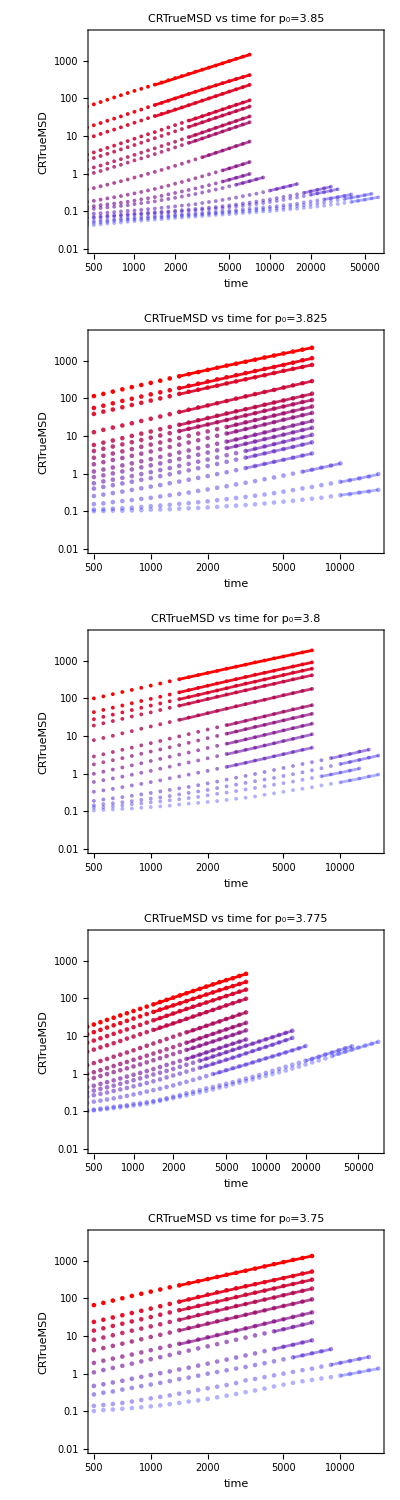

```mathematica
CRTrueMSDMeanPlotsWithFits=Table[Show[
ListLogLogPlot[Table[Table[{time[[p,T,rec+1]]-time[[p,T,1]],CRTrueMSDMean[[p,T,rec]]},{rec,Length[CRTrueMSDMean[[p,T]]]}],{T,Length[temperatures[[p]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]],FrameLabel->{"time","CRTrueMSD"},ImageSize->600,PlotLabel->"CRTrueMSD vs time for p_0="<>ToString[p0s[[p]]],Joined->False,PlotRange->{{500,All},{0.01,5000}},ImageSize->600],ListLogLogPlot[Table[Table[{time[[p,T,t+1]]-time[[p,T,1]],fitsCRTrueMSD[[p,T]][time[[p,T,t+1]]-time[[p,T,Length[trueMSDMean[[p,T]]]-fittingOffsetfromEnd[[p,T]]+1]]]+CRTrueMSDMean[[p,T,Length[trueMSDMean[[p,T]]]-fittingOffsetfromEnd[[p,T]]]]},{t,Length[CRTrueMSDMean[[p,T]]]-fittingOffsetfromEnd[[p,T]]+1,Length[CRTrueMSDMean[[p,T]]]}],{T,Length[temperatures[[p]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]],Joined->True]],{p,Length[p0s]}];
Column[CRTrueMSDMeanPlotsWithFits]
```

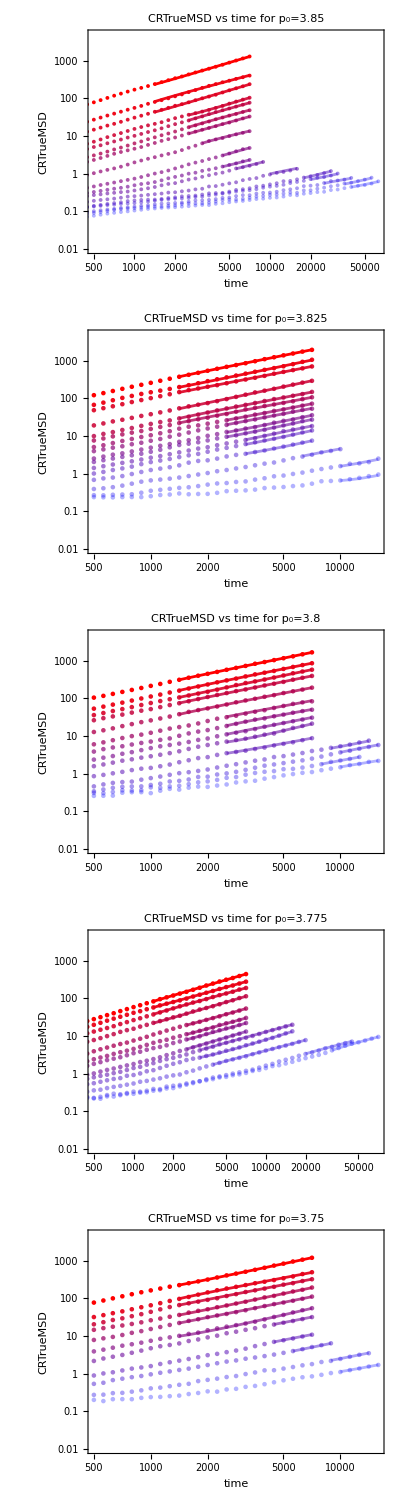

```mathematica
trueMSDMeanPlotsWithFits=Table[Show[
ListLogLogPlot[Table[Table[{time[[p,T,rec+1]]-time[[p,T,1]],trueMSDMean[[p,T,rec]]},{rec,Length[CRTrueMSDMean[[p,T]]]}],{T,Length[temperatures[[p]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]],FrameLabel->{"time","CRTrueMSD"},ImageSize->600,PlotLabel->"CRTrueMSD vs time for p_0="<>ToString[p0s[[p]]],Joined->False,PlotRange->{{500,All},{0.01,5000}},ImageSize->600],ListLogLogPlot[Table[Table[{time[[p,T,t+1]]-time[[p,T,1]],fitsTrueMSD[[p,T]][time[[p,T,t+1]]-time[[p,T,Length[trueMSDMean[[p,T]]]-fittingOffsetfromEnd[[p,T]]+1]]]+trueMSDMean[[p,T,Length[trueMSDMean[[p,T]]]-fittingOffsetfromEnd[[p,T]]]]},{t,Length[CRTrueMSDMean[[p,T]]]-fittingOffsetfromEnd[[p,T]]+1,Length[CRTrueMSDMean[[p,T]]]}],{T,Length[temperatures[[p]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]],Joined->True]],{p,Length[p0s]}];
Column[trueMSDMeanPlotsWithFits]
```

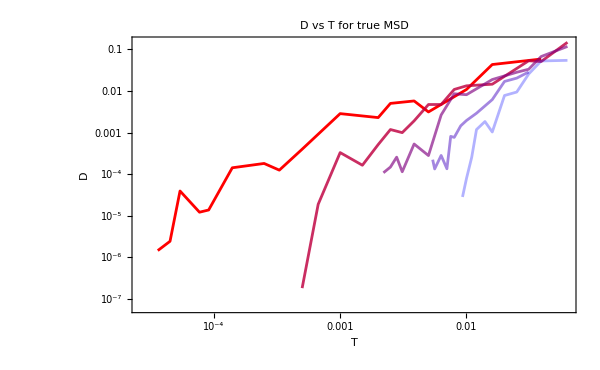

```mathematica
diffusionConstPlots=ListLogLogPlot[Table[Table[{temperatures[[p,T]],fitsTrueMSD[[p,T]]["BestFitParameters"][[1,2]]},{T,Length[temperatures[[p]]]}],{p,Length[p0s]}],PlotStyle->redBluePlotConfig[Length[p0s]],FrameLabel->{"T","D"},PlotLabel->"D vs T for true MSD",Joined->True,ImageSize->600]
```

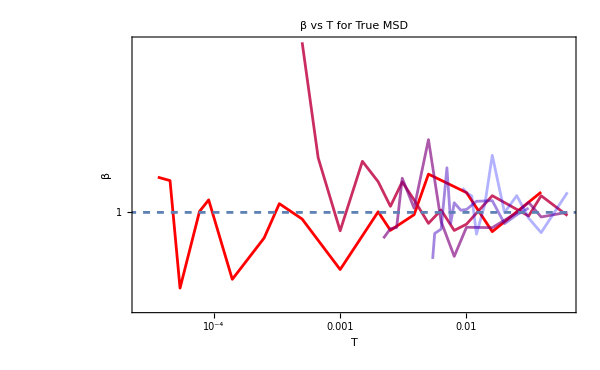

```mathematica
exponenPlots=Show[ListLogLogPlot[Table[Table[{temperatures[[p,T]],fitsTrueMSD[[p,T]]["BestFitParameters"][[2,2]]},{T,Length[temperatures[[p]]]}],{p,Length[p0s]}],PlotStyle->redBluePlotConfig[Length[p0s]],FrameLabel->{"T","β"},PlotLabel->"β vs T for True MSD",Joined->True,ImageSize->600],LogLogPlot[1,{x,0.00001,1},PlotStyle->Dashed]]
```

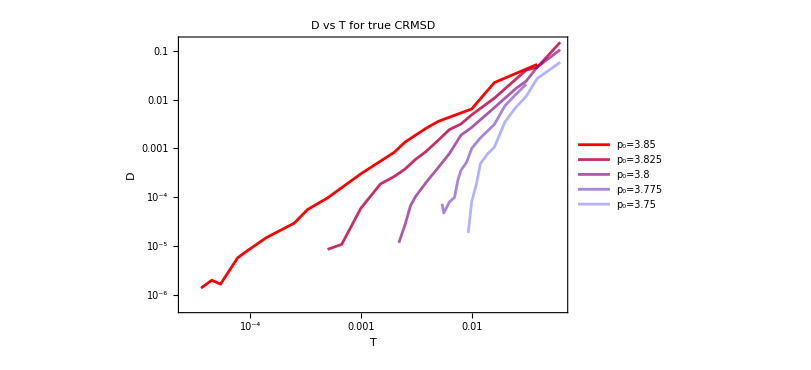

```mathematica
CRdiffusionConstPlots=ListLogLogPlot[Table[Table[{temperatures[[p,T]],fitsCRTrueMSD[[p,T]]["BestFitParameters"][[1,2]]},{T,Length[temperatures[[p]]]}],{p,Length[p0s]}],PlotStyle->redBluePlotConfig[Length[p0s]],FrameLabel->{"T","D"},PlotLabel->"D vs T for true CRMSD",Joined->True,PlotLegends->Table["p_0="<>ToString[p0s[[p]]],{p,Length[p0s]}],ImageSize->600]
```

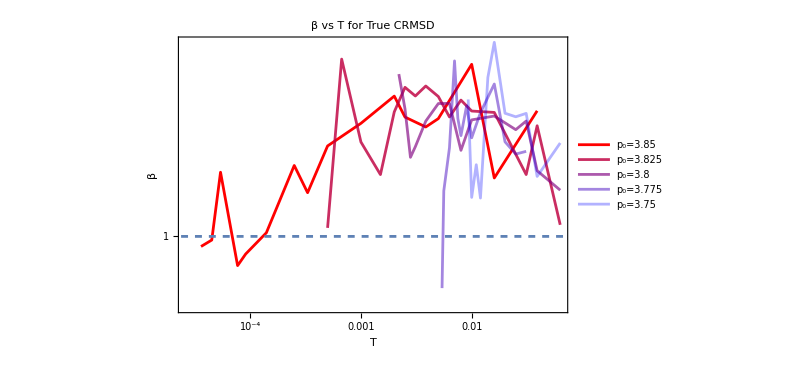

```mathematica
CRexponenPlots=Show[ListLogLogPlot[Table[Table[{temperatures[[p,T]],fitsCRTrueMSD[[p,T]]["BestFitParameters"][[2,2]]},{T,Length[temperatures[[p]]]}],{p,Length[p0s]}],PlotStyle->redBluePlotConfig[Length[p0s]],FrameLabel->{"T","β"},PlotLabel->"β vs T for True CRMSD",PlotLegends->Table["p_0="<>ToString[p0s[[p]]],{p,Length[p0s]}],Joined->True,ImageSize->600],LogLogPlot[1,{x,0.00001,1},PlotStyle->Dashed]]
```

```mathematica
Export["/home/chengling/Research/updates/05232024/MSDfittingNew.jpeg",Grid[Partition[{diffusionConstPlots,CRdiffusionConstPlots,exponenPlots,CRexponenPlots},2]],ImageResolution->800]
```

/home/chengling/Research/updates/05232024/MSDfittingNew.jpeg

```mathematica
Export["/home/chengling/Research/updates/05232024/MSDNew.jpeg",Grid[Partition[{trueMSDMeanPlotsWithFits[[1]],CRTrueMSDMeanPlotsWithFits[[1]],trueMSDMeanPlotsWithFits[[2]],CRTrueMSDMeanPlotsWithFits[[2]],trueMSDMeanPlotsWithFits[[3]],CRTrueMSDMeanPlotsWithFits[[3]]},2]],ImageResolution->800]
```

/home/chengling/Research/updates/05232024/MSDNew.jpeg

### fit it to linear model

```mathematica
LinearFitsCRTrueMSD=Table[Table[LinearModelFit[Table[{time[[p,T,rec+1]]-time[[p,T,Length[trueMSDMean[[p,T]]]-fittingOffsetfromEnd[[p,T]]+1]],CRTrueMSDMean[[p,T,rec]]-CRTrueMSDMean[[p,T,Length[trueMSDMean[[p,T]]]-fittingOffsetfromEnd[[p,T]]]]},{rec,Length[trueMSDMean[[p,T]]]-fittingOffsetfromEnd[[p,T]]+1,Length[trueMSDMean[[p,T]]]}],t,t,IncludeConstantBasis->False],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}}

```mathematica
LinearFitsTrueMSD=Table[Table[LinearModelFit[Table[{time[[p,T,rec+1]]-time[[p,T,Length[trueMSDMean[[p,T]]]-fittingOffsetfromEnd[[p,T]]+1]],trueMSDMean[[p,T,rec]]-trueMSDMean[[p,T,Length[trueMSDMean[[p,T]]]-fittingOffsetfromEnd[[p,T]]]]},{rec,Length[trueMSDMean[[p,T]]]-fittingOffsetfromEnd[[p,T]]+1,Length[trueMSDMean[[p,T]]]}],t,t,IncludeConstantBasis->False],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}}

```mathematica
ToString[t^2]
```

2
t

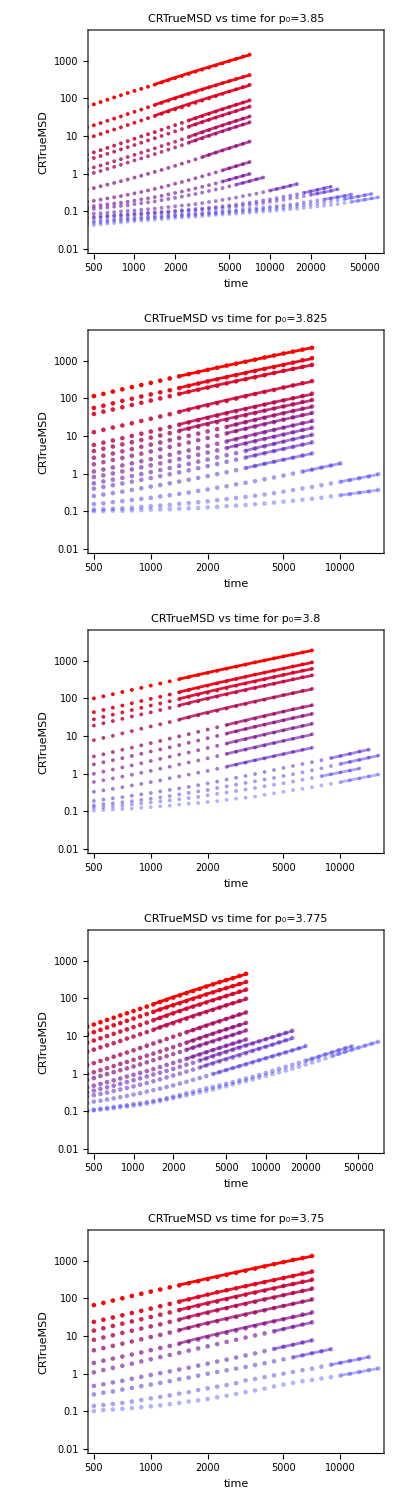

```mathematica
CRTrueMSDMeanPlotsWithLinearFits=Table[Show[
ListLogLogPlot[Table[Table[{time[[p,T,rec+1]]-time[[p,T,1]],CRTrueMSDMean[[p,T,rec]]},{rec,Length[CRTrueMSDMean[[p,T]]]}],{T,Length[temperatures[[p]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]],FrameLabel->{"time","CRTrueMSD"},ImageSize->600,PlotLabel->"CRTrueMSD vs time for p_0="<>ToString[p0s[[p]]],Joined->False,PlotRange->{{500,All},{0.01,5000}},ImageSize->600],ListLogLogPlot[Table[Table[{time[[p,T,t+1]]-time[[p,T,1]],LinearFitsCRTrueMSD[[p,T]][time[[p,T,t+1]]-time[[p,T,Length[trueMSDMean[[p,T]]]-fittingOffsetfromEnd[[p,T]]+1]]]+CRTrueMSDMean[[p,T,Length[trueMSDMean[[p,T]]]-fittingOffsetfromEnd[[p,T]]]]},{t,Length[CRTrueMSDMean[[p,T]]]-fittingOffsetfromEnd[[p,T]]+1,Length[CRTrueMSDMean[[p,T]]]}],{T,Length[temperatures[[p]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]],Joined->True]],{p,Length[p0s]}];
Column[CRTrueMSDMeanPlotsWithLinearFits]
```

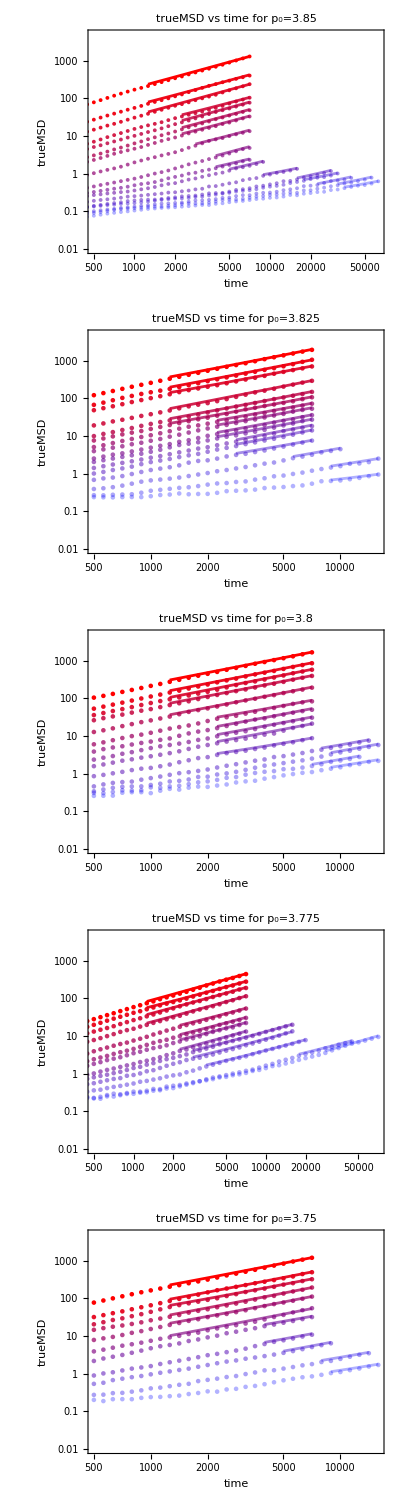

```mathematica
trueMSDMeanPlotsWithLinearFits=Table[Show[
ListLogLogPlot[Table[Table[{time[[p,T,rec+1]]-time[[p,T,1]],trueMSDMean[[p,T,rec]]},{rec,Length[CRTrueMSDMean[[p,T]]]}],{T,Length[temperatures[[p]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]],FrameLabel->{"time","trueMSD"},ImageSize->600,PlotLabel->"trueMSD vs time for p_0="<>ToString[p0s[[p]]],Joined->False,PlotRange->{{500,All},{0.01,5000}},ImageSize->600],ListLogLogPlot[Table[Table[{time[[p,T,t+1]]-time[[p,T,1]],LinearFitsTrueMSD[[p,T]][time[[p,T,t+1]]-time[[p,T,Length[trueMSDMean[[p,T]]]-fittingOffsetfromEnd[[p,T]]]]]+trueMSDMean[[p,T,Length[trueMSDMean[[p,T]]]-fittingOffsetfromEnd[[p,T]]]]},{t,Length[CRTrueMSDMean[[p,T]]]-fittingOffsetfromEnd[[p,T]],Length[CRTrueMSDMean[[p,T]]]}],{T,Length[temperatures[[p]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]],Joined->True]],{p,Length[p0s]}];
Column[trueMSDMeanPlotsWithLinearFits]
```

```mathematica
LinearFitsTrueMSD[[1,1]]["RSquared"]
```

0.999523

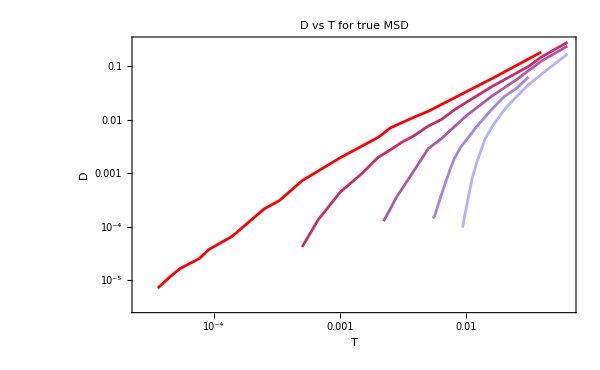

```mathematica
linearFitDiffusionConstPlots=ListLogLogPlot[Table[Table[{temperatures[[p,T]],LinearFitsTrueMSD[[p,T]]["BestFitParameters"][[1]]},{T,Length[temperatures[[p]]]}],{p,Length[p0s]}],PlotStyle->redBluePlotConfig[Length[p0s]],FrameLabel->{"T","D"},PlotLabel->"D vs T for true MSD",Joined->True,ImageSize->600]
```

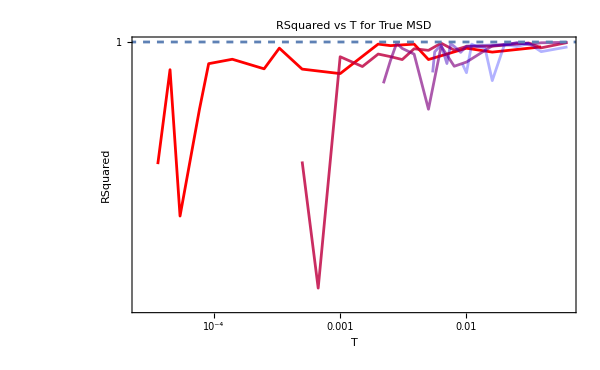

```mathematica
RSMSDPlots=Show[ListLogLogPlot[Table[Table[{temperatures[[p,T]],LinearFitsTrueMSD[[p,T]]["RSquared"]},{T,Length[temperatures[[p]]]}],{p,Length[p0s]}],PlotStyle->redBluePlotConfig[Length[p0s]],FrameLabel->{"T","RSquared"},PlotLabel->"RSquared vs T for True MSD",Joined->True,ImageSize->600,PlotRange->All],LogLogPlot[1,{x,0.00001,1},PlotStyle->Dashed]]
```

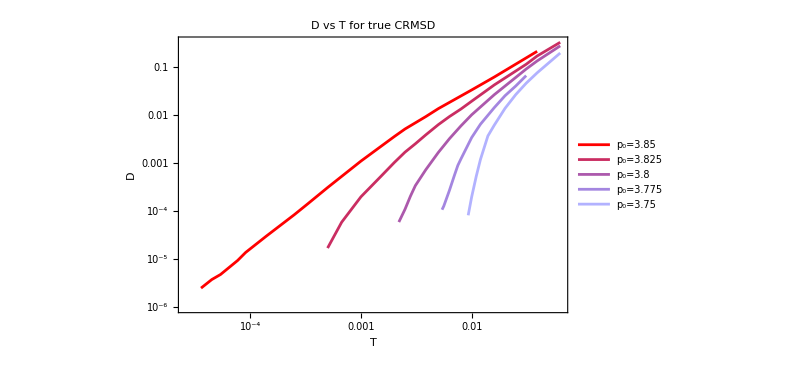

```mathematica
LinearFitCRdiffusionConstPlots=ListLogLogPlot[Table[Table[{temperatures[[p,T]],LinearFitsCRTrueMSD[[p,T]]["BestFitParameters"][[1]]},{T,Length[temperatures[[p]]]}],{p,Length[p0s]}],PlotStyle->redBluePlotConfig[Length[p0s]],FrameLabel->{"T","D"},PlotLabel->"D vs T for true CRMSD",Joined->True,PlotLegends->Table["p_0="<>ToString[p0s[[p]]],{p,Length[p0s]}],ImageSize->600]
```

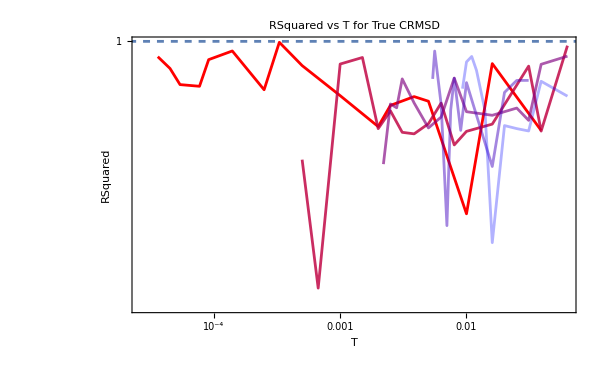

```mathematica
RSCRMSDPlots=Show[ListLogLogPlot[Table[Table[{temperatures[[p,T]],LinearFitsCRTrueMSD[[p,T]]["RSquared"]},{T,Length[temperatures[[p]]]}],{p,Length[p0s]}],PlotStyle->redBluePlotConfig[Length[p0s]],FrameLabel->{"T","RSquared"},PlotLabel->"RSquared vs T for True CRMSD",Joined->True,ImageSize->600,PlotRange->All],LogLogPlot[1,{x,0.00001,1},PlotStyle->Dashed]]
```

```mathematica
Export["/home/chengling/Research/updates/05232024/MSDLinearfitting.jpeg",Grid[Partition[{linearFitDiffusionConstPlots,LinearFitCRdiffusionConstPlots,RSMSDPlots,RSCRMSDPlots},2]],ImageResolution->800]
```

/home/chengling/Research/updates/05232024/MSDLinearfitting.jpeg

```mathematica
Export["/home/chengling/Research/updates/05232024/MSDwithLinearfitting.jpeg",Grid[Partition[{trueMSDMeanPlotsWithLinearFits[[1]],CRTrueMSDMeanPlotsWithLinearFits[[1]],trueMSDMeanPlotsWithLinearFits[[2]],CRTrueMSDMeanPlotsWithLinearFits[[2]],trueMSDMeanPlotsWithLinearFits[[3]],CRTrueMSDMeanPlotsWithLinearFits[[3]]},2]],ImageResolution->800]
```

/home/chengling/Research/updates/05232024/MSDwithLinearfitting.jpeg